```mathematica
Data=Import[NotebookDirectory[]<>"SimData.mat"];
```

```mathematica
colorf=Module[{colorlist},colorlist=Get[NotebookDirectory[]<>"ColorCode.txt"];
Evaluate[Blend[RGBColor@@@colorlist,#]&]];
```

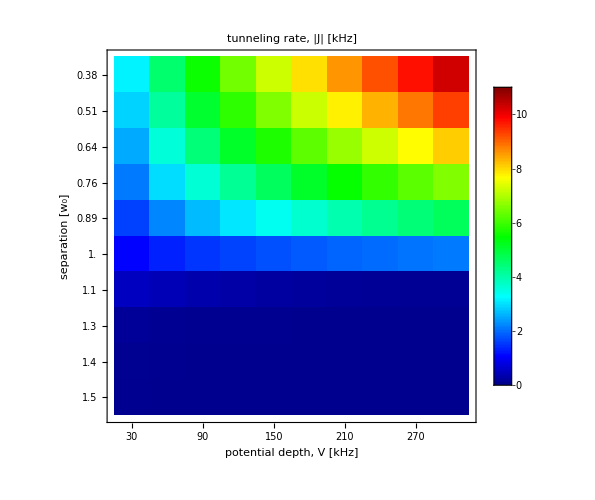
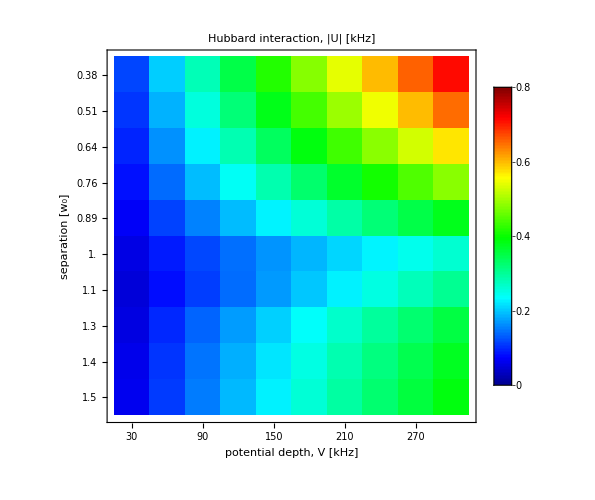
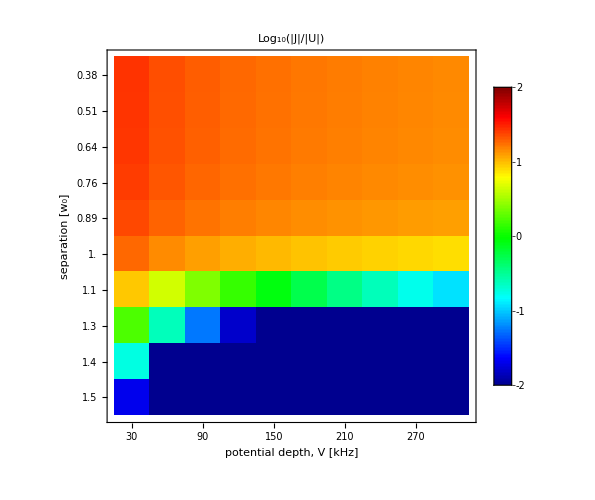
-Graphics- | -Graphics- | -Graphics-

```mathematica
xticks=Table[{i,NumberForm[Data⟦4⟧⟦i⟧⟦1⟧,2]},{i,1,Length[Data⟦2⟧]}];
yticks=Table[{i,NumberForm[Round[Data⟦3⟧⟦i⟧⟦1⟧/1000],3]},{i,1,Length[Data⟦2⟧]}];

AxslblSz=20;
imgsz=500;


ExportPlot=Grid[{{
MatrixPlot[Abs[Data⟦1⟧],FrameTicks->{xticks,yticks},FrameLabel->{"separation [w_0]","potential depth, V [kHz]"},FrameStyle->Directive[{Thick,Black,AxslblSz}],PlotLabel->Style["tunneling rate, |J| [kHz]",Black,AxslblSz],ImageSize->imgsz,ColorFunctionScaling->False,ColorFunction->Function[{z},colorf[z/11]],PlotLegends->BarLegend[{Function[{z},colorf[z/11]],{0,11}},LegendMarkerSize->500,LabelStyle->Directive[{Thick,Black,AxslblSz}]]],

MatrixPlot[Abs[Data⟦2⟧],FrameTicks->{xticks,yticks},FrameLabel->{"separation [w_0]","potential depth, V [kHz]"},FrameStyle->Directive[{Thick,Black,AxslblSz}],PlotLabel->Style["Hubbard interaction, |U| [kHz]",Black,AxslblSz],ImageSize->imgsz,ColorFunctionScaling->False,ColorFunction->Function[{z},colorf[z/0.8]],PlotLegends->BarLegend[{Function[{z},colorf[z/0.8]],{0,0.8}},LegendMarkerSize->500,LabelStyle->Directive[{Thick,Black,AxslblSz}]]],

MatrixPlot[Log[10,Abs[Data⟦1⟧/Data⟦2⟧]],FrameTicks->{xticks,yticks},FrameLabel->{"separation [w_0]","potential depth, V [kHz]"},FrameStyle->Directive[{Thick,Black,AxslblSz}],PlotLabel->Style["Log_10(|J|/|U|)",Black,AxslblSz],ImageSize->imgsz,ColorFunctionScaling->False,ColorFunction->Function[{z},colorf[(z+2)/4]],PlotLegends->BarLegend[{Function[{z},colorf[(z+2)/4]],{-2,2}},LegendMarkerSize->500,LabelStyle->Directive[{Thick,Black,AxslblSz}]]]
}}]
```

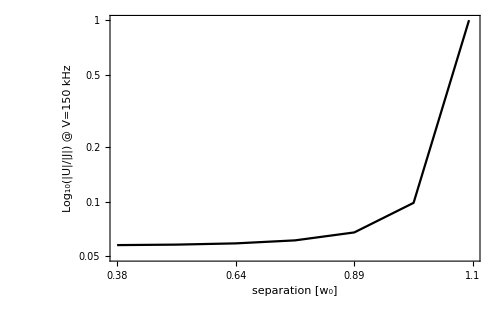

```mathematica
ExportPlot2=ListLogPlot[Abs[Data⟦2⟧/Data⟦1⟧]ᵀ⟦5⟧,PlotRange->{{1,7},{0.05,1}},Joined->True,PlotStyle->Black,Frame->True,FrameTicks->{{Automatic,None},{xticks,None}},FrameLabel->{"separation [w_0]","Log_10(|U|/|J|) @ V=150 kHz"},FrameStyle->Directive[{Thick,Black,AxslblSz}],ImageSize->imgsz]
```

```mathematica
Export[NotebookDirectory[]<>"HubbardInteractionAndTunneling.png",ExportPlot];
Export[NotebookDirectory[]<>"HubbardInteractionAndTunneling.pdf",ExportPlot];
Export[NotebookDirectory[]<>"UvsJforV150kHz.png",ExportPlot2];
Export[NotebookDirectory[]<>"UvsJforV150kHz.pdf",ExportPlot2];
```